# Лабораторная работа №8

## Выполнил студент группы 0В92 Кандыбо Андрей

## 1

В файле “Данные” на листах “РС”, “CC”, “ИС” приведены экономические показатели предприятий пищевой промышленности России за 2012 – 2016 годы различных форм собственности.  Для указанных в варианте задания типа собственности предприятий, года анализа и группы экономических показателей требуется:

1.	Используя метод главных компонент, перейти от пространства исходных признаков (показателей) к факторному пространству главных компонент, объясняющих не менее 70% вариации исходных признаков. 
2.	Провести иерархическую кластеризацию предприятий на основе построенных главных компонент, используя алгоритм Варда (выбрать в качестве меры близости объектов квадрат евклидова расстояния).
3.	На основе, полученной в результате кластеризации дендрограммы, выбрать оптимальное разбиение совокупности объектов на кластеры. В качестве оптимального разбиения выбрать множество кластеров, для которого: 1) по каждому фактору (главной компоненте) средние значения фактора по кластерам для всей совокупности кластеров значимо различаются; 2) для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора (главной компоненты); 3) для любого другого разбиения с большим числом кластеров условия 1 или 2 не выполняются. Для анализа различий средних по кластерам использовать методы дисперсионного анализа.  Для получения устойчивого разбиения, соответствующего условиям 1-3, выбрать подходящий критерий множественного сравнения (Дункана, Бонферрони и др.), а также при необходимости подобрать уровень значимости критерия. 
4.	Провести кластеризацию той же совокупности, используя алгоритм k-средних, положив число кластеров, равным, полученному числу кластеров на предыдущем этапе.  Оценить качество кластеризации, используя дисперсионный анализ (проверить для полученного разбиения выполнение условий 1-2 предыдущего раздела).
5.	Сравнить полученные в пунктах 3 и 4 разбиения, используя в качестве функционала качества разбиения сумму средних квадратов расстояний до центров кластеров.

```mathematica
X= Import["C:\\Users\\71380279\\Desktop\\data_1.xlsx"][[2;;,2;;]];
```

```mathematica
X[[;;4,;;]]
```

{{1.02025×10^9,1.78336×10^8,9.1825×10^7,6.7596×10^7,0.0711,0.0121,0.6193,0.0119,5.39917×10^9,9.0776×10^7},{3.35373×10^9,1.5949×10^9,9.8456×10^7,7.67107×10^8,0.0172,0.1571,0.0899,0.1358,3.38701×10^9,7.2671×10^7},{1.6484×10^9,8.03278×10^8,1.0444×10^7,-2.2632×10^7,0.0016,-0.004,0.0021,-0.004,5.64731×10^9,4.013×10^6},{1.18114×10^9,3.31585×10^8,8.7255×10^7,7.8×10^7,0.0282,0.0143,0.0324,0.0141,4.35326×10^9,6.1533×10^7}}

### Перейдем от пространства исходных признаков к факторному пространству главных компонент

```mathematica
X0:=Standardize[X]
```

```mathematica
n:=Length[X]
```

```mathematica
k:=Length[X[[1]]]
```

```mathematica
A = Covariance[X0];
A//MatrixForm
```

(1. | 0.218286 | 0.00545802 | 0.331195 | -0.142732 | 0.256818 | -0.192764 | 0.265484 | -0.0255435 | 0.0010906
0.218286 | 1. | -0.0258992 | 0.138878 | -0.0340169 | 0.193178 | -0.109255 | 0.118227 | -0.0102348 | -0.00720147
0.00545802 | -0.0258992 | 1. | 0.703815 | 0.74171 | 0.651377 | -0.119375 | 0.688505 | -0.327951 | 0.994403
0.331195 | 0.138878 | 0.703815 | 1. | 0.439213 | 0.948324 | 0.0748003 | 0.973426 | -0.522125 | 0.664285
-0.142732 | -0.0340169 | 0.74171 | 0.439213 | 1. | 0.405986 | -0.0458309 | 0.427929 | -0.206817 | 0.768099
0.256818 | 0.193178 | 0.651377 | 0.948324 | 0.405986 | 1. | 0.131114 | 0.983476 | -0.616913 | 0.615922
-0.192764 | -0.109255 | -0.119375 | 0.0748003 | -0.0458309 | 0.131114 | 1. | 0.0941871 | -0.123412 | -0.154871
0.265484 | 0.118227 | 0.688505 | 0.973426 | 0.427929 | 0.983476 | 0.0941871 | 1. | -0.624014 | 0.651084
-0.0255435 | -0.0102348 | -0.327951 | -0.522125 | -0.206817 | -0.616913 | -0.123412 | -0.624014 | 1. | -0.302408
0.0010906 | -0.00720147 | 0.994403 | 0.664285 | 0.768099 | 0.615922 | -0.154871 | 0.651084 | -0.302408 | 1.)

```mathematica
Λ=Eigenvalues[A]
```

{4.92084,1.59597,1.32024,0.834199,0.686635,0.367765,0.227011,0.0379193,0.00686785,0.00255493}

```mathematica
Table[Sum[Λ[[i]]/k,{i,1,j}],{j,1,k}]
```

{0.492084,0.651681,0.783705,0.867125,0.935788,0.972565,0.995266,0.999058,0.999745,1.}

Заметим, что первые 3 признаков объясняют 78% исходных признаков, оставим их в качестве главных компонент.

```mathematica
m=3;
```

```mathematica
vec=Eigenvectors[A];
```

```mathematica
β={vec[[1]],vec[[2]],vec[[3]]}
```

{{0.0852822,0.0474887,0.394349,0.419283,0.296699,0.414547,0.00425998,0.423547,-0.267615,0.385038},{-0.524953,-0.38444,0.305569,-0.200157,0.44395,-0.234549,-0.0876312,-0.200462,0.185774,0.329718},{-0.381483,-0.343898,-0.143002,0.0357775,-0.100069,0.117895,0.724655,0.106515,-0.347677,-0.182243}}

```mathematica
F=X0.Transpose[β];
```

```mathematica
F[[;;10,;;]]
```

{{-1.86883,1.31803,0.427066},{0.653422,-1.47412,-0.815693},{-2.29225,0.904018,-1.44366},{-1.58711,1.01311,-0.54198},{-1.18016,1.075,-0.713611},{-2.56177,0.18158,-2.00561},{-0.919175,0.782043,0.195594},{-1.34188,0.359933,-0.938834},{-1.10003,0.696342,-0.431018},{-0.196807,-0.339789,-0.154458}}

### Проведем иерархическую кластеризацию на основе построенных главных компонент

```mathematica
Needs["HierarchicalClustering`"]
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

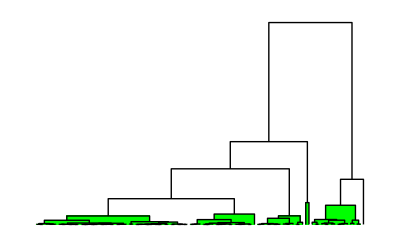

```mathematica
NCL=Range[1,n];
F0=MapThread[#1->#2&,{F,NCL}];
AC=Agglomerate[F0,Linkage->"Ward"];
DendrogramPlot[AC,HighlightLevel->6]
```

### Выберем оптимальное разбиение совокупности объектов на кластеры

```mathematica
q=20;
```

```mathematica
Q=ClusterSplit[AC,q];
Q1=Table[If[IntegerQ[Q[[i]]],{Q[[i]]},Sort[ClusterFlatten[Q[[i]]]]],{i,1,q}]
```

{{1,52,60,69,73,78,79},{7,9,14,15,23,28,29,35,46,54,58,63,65,67,71,87,90,91,93,96,99,101},{3,6},{4,5,12,16,17,22,30,31,34,59,61},{8,25,41,48,56,75},{72,82,89,94},{10,11,33,37,40,47,51,62,77,81,83,84,88,95,102,103},{43},{2,26,38,42,53,74,85,100},{18,19,20,68},{32,44,45},{66},{76},{92},{70,98},{21,36,55,57,80},{24,27,50,64},{13,86},{49,97},{39}}

```mathematica
Z=ConstantArray[0,n];
For[i=1,i≤q,i++,
For[j=1,j≤Length[Q1[[i]]],j++,
Z[[Q1[[i,j]]]]=i]]
Z
```

{1,9,3,4,4,3,2,5,2,7,7,4,18,2,2,4,4,10,10,10,16,4,2,17,5,9,17,2,2,4,4,11,7,4,2,16,7,9,20,7,5,9,8,11,11,2,7,5,19,17,7,1,9,2,16,5,16,2,4,1,4,7,2,17,2,12,2,10,1,15,2,6,1,9,5,13,7,1,1,16,7,6,7,7,9,18,2,7,6,2,2,14,2,6,7,2,19,15,2,9,2,7,7}

```mathematica
FZ1=MapThread[{#1,#2}&,{Z,F[[All,1]]}];
FZ2=MapThread[{#1,#2}&,{Z,F[[All,2]]}];
FZ3=MapThread[{#1,#2}&,{Z,F[[All,3]]}];
```

```mathematica
Needs["ANOVA`"]
```

```mathematica
an1 = ANOVA[FZ1,PostTests->Bonferroni,CellMeans->False];
an2 = ANOVA[FZ2,PostTests->Bonferroni,CellMeans->False];
an3 = ANOVA[FZ3,PostTests->Bonferroni,CellMeans->False];
```

```mathematica
an3
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 122.349 | 6.43944 | 43.3995 | 4.12837×10^-35
Error | 83 | 12.3152 | 0.148376 |  | 
Total | 102 | 134.665 |  |  | ,PostTests→{Model→Bonferroni | {{1,2},{1,3},{2,3},{1,4},{3,4},{1,5},{2,5},{2,6},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{6,9},{7,9},{8,9},{1,10},{2,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{1,11},{2,11},{4,11},{6,11},{7,11},{8,11},{1,12},{2,12},{3,12},{4,12},{5,12},{6,12},{7,12},{9,12},{10,12},{11,12},{1,13},{2,13},{6,13},{7,13},{8,13},{12,13},{1,14},{2,14},{3,14},{4,14},{5,14},{7,14},{9,14},{10,14},{11,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{5,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{3,16},{4,16},{5,16},{6,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{14,16},{15,16},{3,17},{4,17},{5,17},{8,17},{9,17},{10,17},{11,17},{12,17},{13,17},{14,17},{15,17},{3,18},{5,18},{8,18},{10,18},{11,18},{12,18},{13,18},{14,18},{15,18},{3,19},{6,19},{8,19},{10,19},{11,19},{12,19},{13,19},{14,19},{15,19},{1,20},{2,20},{4,20},{6,20},{7,20},{8,20},{9,20},{12,20},{14,20},{15,20},{16,20},{17,20},{18,20},{19,20}}}}

```mathematica
an1[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 488.47 | 25.7089 | 158.581 | 5.5853×10^-57
Error | 83 | 13.4558 | 0.162118 |  | 
Total | 102 | 501.926 |  |  |

```mathematica
pv1 = %[[1,5]];
```

```mathematica
an2[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 150.606 | 7.92664 | 54.0032 | 1.16872×10^-38
Error | 83 | 12.1828 | 0.146781 |  | 
Total | 102 | 162.789 |  |  |

```mathematica
pv2 = %[[1,5]];
```

```mathematica
an3[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 122.349 | 6.43944 | 43.3995 | 4.12837×10^-35
Error | 83 | 12.3152 | 0.148376 |  | 
Total | 102 | 134.665 |  |  |

```mathematica
pv3 = %[[1,5]];
```

```mathematica
pv={pv1,pv2,pv3}
```

{5.5853×10^-57,1.16872×10^-38,4.12837×10^-35}

```mathematica
a1=an1[[2,2]][[1,2]]
```

Bonferroni | {{2,3},{2,4},{3,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{1,9},{2,9},{3,9},{4,9},{5,9},{3,10},{7,10},{9,10},{1,11},{2,11},{3,11},{4,11},{5,11},{10,11},{1,12},{2,12},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{9,12},{10,12},{11,12},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{1,14},{2,14},{3,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{5,15},{6,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15},{1,16},{2,16},{3,16},{4,16},{5,16},{6,16},{7,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{1,17},{2,17},{3,17},{4,17},{5,17},{6,17},{7,17},{8,17},{9,17},{10,17},{12,17},{13,17},{14,17},{16,17},{1,18},{2,18},{3,18},{4,18},{5,18},{6,18},{7,18},{8,18},{9,18},{10,18},{11,18},{12,18},{13,18},{15,18},{16,18},{17,18},{1,19},{2,19},{3,19},{4,19},{5,19},{6,19},{7,19},{8,19},{9,19},{10,19},{11,19},{12,19},{13,19},{15,19},{17,19},{18,19},{1,20},{2,20},{3,20},{4,20},{5,20},{6,20},{7,20},{8,20},{9,20},{10,20},{11,20},{12,20},{13,20},{14,20},{15,20},{16,20},{17,20},{19,20}}

```mathematica
a1=%[[1,2]];
```

```mathematica
a2=an2[[2,2]][[1,2]]
```

Bonferroni | {{1,5},{4,5},{1,7},{2,7},{4,7},{6,7},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{1,11},{2,11},{3,11},{4,11},{5,11},{6,11},{7,11},{8,11},{9,11},{10,11},{1,12},{2,12},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{9,12},{10,12},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{11,14},{12,14},{13,14},{11,15},{12,15},{13,15},{1,16},{2,16},{4,16},{6,16},{11,16},{12,16},{13,16},{1,17},{4,17},{6,17},{9,17},{11,17},{12,17},{13,17},{1,18},{2,18},{3,18},{4,18},{5,18},{6,18},{7,18},{8,18},{11,18},{12,18},{1,19},{2,19},{3,19},{4,19},{5,19},{6,19},{7,19},{8,19},{9,19},{10,19},{14,19},{15,19},{16,19},{17,19},{1,20},{2,20},{3,20},{4,20},{5,20},{6,20},{7,20},{8,20},{9,20},{10,20},{11,20},{12,20},{13,20},{14,20},{15,20},{16,20},{17,20},{18,20},{19,20}}

```mathematica
a2=%[[1,2]];
```

```mathematica
a3=an3[[2,2]][[1,2]]
```

Bonferroni | {{1,2},{1,3},{2,3},{1,4},{3,4},{1,5},{2,5},{2,6},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{6,9},{7,9},{8,9},{1,10},{2,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{1,11},{2,11},{4,11},{6,11},{7,11},{8,11},{1,12},{2,12},{3,12},{4,12},{5,12},{6,12},{7,12},{9,12},{10,12},{11,12},{1,13},{2,13},{6,13},{7,13},{8,13},{12,13},{1,14},{2,14},{3,14},{4,14},{5,14},{7,14},{9,14},{10,14},{11,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{5,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{3,16},{4,16},{5,16},{6,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{14,16},{15,16},{3,17},{4,17},{5,17},{8,17},{9,17},{10,17},{11,17},{12,17},{13,17},{14,17},{15,17},{3,18},{5,18},{8,18},{10,18},{11,18},{12,18},{13,18},{14,18},{15,18},{3,19},{6,19},{8,19},{10,19},{11,19},{12,19},{13,19},{14,19},{15,19},{1,20},{2,20},{4,20},{6,20},{7,20},{8,20},{9,20},{12,20},{14,20},{15,20},{16,20},{17,20},{18,20},{19,20}}

```mathematica
a3=%[[1,2]];
```

```mathematica
a=Sort[DeleteDuplicates[Join[a1,a2,a3]]];
```

```mathematica
okey = True;
```

```mathematica
If[Sum[If[pv[[i]]<0.05,0,1],{i,1,m}]==0,{Print["По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"]},{Print["Не по каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"],okey=False;}];
```

По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются

```mathematica
If[Length[a]==Sum[i,{i,1,q-1}],{Print["Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора"]},{Print["Для ",Abs[Length[a]-Sum[i,{i,1,q-1}] ]," пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора"],okey=False;}];
```

Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора

```mathematica
Print[If[okey,"Количество кластеров не превышает оптимальное значение","Следует уменьшить число кластеров"]]
```

Количество кластеров не превышает оптимальное значение

Начал с количества кластеров q = 6, дальше увеличивал это значение, пока не достиг оптимального, такого, что для (q+1) кластеров не будет являться оптимальным

В ходе подбора оптимального количества кластеров, получили значение q = 20

### Проведем кластеризацию методом k-средних, количество кластеров возьмем равным q=20 - значение, которое является оптимальным для предыдущего метода.

```mathematica
CL=FindClusters[F0,q,Method->"KMeans", DistanceFunction->EuclideanDistance]
```

{{1,17,52,60},{2,26,32,38,42,44,53,74,85},{3,6,30},{4,5,12,16,22,34},{7,46,73,78,79,99},{8,9,25,31,41,54,56,58,59,61,63,65,96},{10,83,100,103},{11,27,33,51,62,81,95,102},{13,49,57,86,92,97},{14,15,28,29},{18,19,68},{20,45},{21,24,36,50,55,64,70,80,98},{23,35,37,67,71,77,87,88,90,91,93,101},{39},{40,48,75,84},{43},{47},{66,76},{69,72,82,89,94}}

```mathematica
Z=ConstantArray[0,n];
For[i=1,i≤q,i++,
For[j=1,j≤Length[CL[[i]]],j++,
Z[[CL[[i,j]]]]=i]]
Z
```

{1,2,3,4,4,3,5,6,6,7,8,4,9,10,10,4,1,11,11,12,13,4,14,13,6,2,8,10,10,3,6,2,8,4,14,13,14,2,15,16,6,2,17,2,12,5,18,16,9,13,8,1,2,6,13,6,9,6,6,1,6,8,6,13,6,19,14,11,20,13,14,20,5,2,16,19,14,5,5,13,8,20,7,16,2,9,14,14,20,14,14,9,14,20,8,6,9,13,5,7,14,8,7}

```mathematica
FZ11=MapThread[{#1,#2}&,{Z,F[[All,1]]}];
FZ21=MapThread[{#1,#2}&,{Z,F[[All,2]]}];
FZ31=MapThread[{#1,#2}&,{Z,F[[All,3]]}];
```

```mathematica
km1 = ANOVA[FZ11,PostTests->Bonferroni,CellMeans->False];
km2 = ANOVA[FZ21,PostTests->Bonferroni,CellMeans->False];
km3 = ANOVA[FZ31,PostTests->Bonferroni,CellMeans->False];
```

```mathematica
km1[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 476.856 | 25.0977 | 83.0949 | 7.49625×10^-46
Error | 83 | 25.0691 | 0.302037 |  | 
Total | 102 | 501.926 |  |  |

```mathematica
pv11 = %[[1,5]];
```

```mathematica
km2[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 140.795 | 7.41027 | 27.9648 | 2.96906×10^-28
Error | 83 | 21.9938 | 0.264985 |  | 
Total | 102 | 162.789 |  |  |

```mathematica
pv21 = %[[1,5]];
```

```mathematica
km3[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 19 | 91.8222 | 4.83275 | 9.36265 | 1.1449×10^-13
Error | 83 | 42.8423 | 0.516173 |  | 
Total | 102 | 134.665 |  |  |

```mathematica
pv31 = %[[1,5]];
```

```mathematica
pv0={pv1,pv2,pv3}
```

{5.5853×10^-57,1.16872×10^-38,4.12837×10^-35}

```mathematica
k1=km1[[2,2]][[1,2]]
```

Bonferroni | {{1,2},{2,3},{2,4},{2,5},{2,6},{1,7},{3,7},{1,8},{3,8},{4,8},{5,8},{6,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{2,10},{3,10},{9,10},{2,11},{8,11},{9,11},{3,12},{9,12},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{1,14},{2,14},{3,14},{8,14},{9,14},{13,14},{1,15},{2,15},{3,15},{4,15},{5,15},{6,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15},{2,16},{3,16},{9,16},{13,16},{15,16},{9,17},{13,17},{15,17},{9,18},{13,18},{15,18},{1,19},{2,19},{3,19},{4,19},{5,19},{6,19},{7,19},{8,19},{9,19},{10,19},{11,19},{12,19},{13,19},{14,19},{15,19},{16,19},{17,19},{18,19},{1,20},{3,20},{4,20},{9,20},{13,20},{15,20},{19,20}}

```mathematica
k1=%[[1,2]];
```

```mathematica
k2=km2[[2,2]][[1,2]]
```

Bonferroni | {{1,2},{2,3},{2,4},{2,5},{2,6},{2,7},{4,7},{2,8},{1,9},{3,9},{4,9},{5,9},{6,9},{8,9},{2,10},{9,10},{1,11},{4,11},{5,11},{10,11},{1,12},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{10,12},{11,12},{1,13},{2,13},{4,13},{5,13},{6,13},{10,13},{12,13},{2,14},{9,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{5,15},{6,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15},{2,16},{9,16},{12,16},{15,16},{2,17},{9,17},{12,17},{15,17},{15,18},{1,19},{2,19},{3,19},{4,19},{5,19},{6,19},{7,19},{8,19},{9,19},{10,19},{11,19},{13,19},{14,19},{15,19},{16,19},{17,19},{18,19},{2,20},{9,20},{11,20},{12,20},{13,20},{15,20},{19,20}}

```mathematica
k2=%[[1,2]];
```

```mathematica
k3=km3[[2,2]][[1,2]]
```

Bonferroni | {{2,8},{3,8},{2,9},{3,9},{1,11},{8,11},{9,11},{1,12},{5,12},{8,12},{9,12},{2,13},{3,13},{6,13},{11,13},{12,13},{11,14},{12,14},{9,15},{13,15},{1,17},{2,17},{3,17},{4,17},{5,17},{6,17},{7,17},{8,17},{9,17},{10,17},{11,17},{12,17},{13,17},{14,17},{15,17},{16,17},{2,19},{3,19},{4,19},{6,19},{11,19},{12,19},{15,19},{2,20},{3,20},{4,20},{6,20},{10,20},{11,20},{12,20},{15,20},{16,20}}

```mathematica
k3=%[[1,2]];
```

```mathematica
k0=Sort[DeleteDuplicates[Join[a1,a2,a3]]];
```

```mathematica
ok1=0;
ok2=0;
```

```mathematica
If[Sum[If[pv0[[i]]<0.05,0,1],{i,1,m}]==0,{Print["По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"]},{Print["Не по каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"],ok1=1;}];
```

По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются

```mathematica
If[Length[k0]==Sum[i,{i,1,q-1}],{Print["Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора"]},{Print["Для ",Abs[Length[k0]-Sum[i,{i,1,q-1}] ]," пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора"],okey=False;}];
```

Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора

```mathematica
Print[If[ok1+ok2 == 0,"Условия 1 и 2 выполняются",If[And[ok1==1,ok2==0],Print["Условие 1 не выполняется"],If[And[ok1==0,ok2==1],Print["Условие 2 не выполняется"], Print["Оба условия не выполняются"]]]]]
```

Условия 1 и 2 выполняются

### Сравним два полученных разбиения

```mathematica
FW1=Table[F[[Q1[[i]]]],{i,1,q}];
FW2=Table[F[[CL[[i]]]],{i,1,q}];
```

```mathematica
FW1means=Table[Mean[FW1[[i]]],{i,1,q}]
FW2means=Table[Mean[FW2[[i]]],{i,1,q}]
```

{{-1.38832,0.929381,0.72041},{-0.761579,0.545617,-0.0701867},{-2.42701,0.542799,-1.72464},{-1.58843,0.913156,-0.520999},{-1.12377,0.111284,-0.751124},{0.0947023,0.947791,1.46601},{0.165705,0.0343175,0.286114},{-0.664006,0.927266,4.3869},{0.581268,-1.11648,-0.68953},{-0.90404,-1.05141,-1.78888},{0.932197,-3.15707,-1.60713},{-9.13078,-4.33861,5.18211},{-5.59665,-2.6487,-1.82885},{4.56844,-0.52912,2.47668},{2.45202,0.0115809,2.09507},{3.53143,-0.538948,0.429439},{1.89088,-0.183024,0.521546},{6.40835,-1.26307,0.457667},{4.38205,-2.68113,-0.0131467},{7.79912,5.84243,-2.28982}}

{{-1.85901,1.07299,0.488779},{0.856543,-1.53959,-0.918244},{-2.34506,0.772578,-1.41856},{-1.42185,0.968904,-0.561525},{-1.16455,0.761032,0.292217},{-1.20983,0.435912,-0.494345},{-0.207076,-0.313973,0.0532044},{0.684832,0.0328349,0.452852},{5.07949,-1.44629,0.723319},{-0.40674,0.800578,-0.524594},{-1.04749,-0.774397,-1.62626},{-0.422009,-2.80849,-2.10428},{2.67672,-0.418387,0.802655},{-0.462915,0.489639,0.270364},{7.79912,5.84243,-2.28982},{-0.426016,-0.0224641,-0.577843},{-0.664006,0.927266,4.3869},{-0.205605,-0.695627,0.966576},{-7.36371,-3.49366,1.67663},{-0.107761,0.90038,1.4087}}

Сумма средних квадратов расстояния до центров кластеров для разбиения, полученного с помощью метода Варда:

```mathematica
FW1MS=Sum[Mean[Table[Norm[(FW1[[j,i]]-FW1means[[j]])^2],{i,1,Length[FW1[[j]]]}]],{j,1,q}]
```

4.83262

Сумма средних квадратов расстояния до центров кластеров для разбиения, полученного методом k-средних:

```mathematica
FW2MS=Sum[Mean[Table[Norm[(FW2[[j,i]]-FW2means[[j]])^2],{i,1,Length[FW2[[j]]]}]],{j,1,q}]
```

20.0477

## Вывод :

В среднем квадрат расстояния до центра кластера при кластеризации методом k - средних получился значительно больше, чем та же метрика при кластеризации с использованием алгоритма Варда . Следовательно Метод Варда более точно разделяет наблюдения на кластеры в смысле метрики заданной выше .